Φ(R0)        = 0.

Φ'(R0)       = 0

Φ''(R0)      = 0.005

BD residual at r = R0:   0

BD residual at r = 2R0:  -1.832137418190281680794316499415026089769824601412259712235526754150660064350481×10^-42

BD residual at r = 5R0:  -1.7204085110773246237335907363391645921536046030402628872867414563716772522200865×10^-692

BD residual at r = 10R0: -1.1949333428024287265618479296749862191063741718780814308364916376535849205648241×10^-3514

Limit r→∞ BD residual:   0

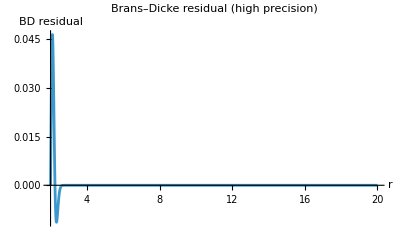

```mathematica
(*--------------------------------------------*)(*1. Parameters and scalar potential*)(*--------------------------------------------*)ClearAll["Global`*"];

R0=SetPrecision[2.0,80];
w=SetPrecision[0.2,80];
A=SetPrecision[0.01,80];

Phi[r_]:=Module[{rr=SetPrecision[r,80]},-A (1-R0/rr) Exp[-(rr-R0)^2/w^2]]

(*--------------------------------------------*)
(*2. BD scalar field equation residual*)
(*phi''+2 phi'/r=0*)
(*--------------------------------------------*)

BDResidual[r_]:=Module[{rr,dp,ddp},rr=SetPrecision[r,80];
dp=SetPrecision[D[Phi[x],x]/. x->rr,80];
ddp=SetPrecision[D[Phi[x],{x,2}]/. x->rr,80];
SetPrecision[ddp+(2/rr) dp,80]]

(*--------------------------------------------*)
(*3. Evaluate at throat and far outside*)
(*--------------------------------------------*)

Print["Φ(R0)        = ",Phi[R0]];
Print["Φ'(R0)       = ",BDResidual[R0]/. (_+_/R0)->N[D[Phi[x],x]/. x->R0]];
Print["Φ''(R0)      = ",N[D[Phi[x],{x,2}]/. x->R0]];

Print["BD residual at r = R0:   ",BDResidual[R0]];
Print["BD residual at r = 2R0:  ",BDResidual[2 R0]];
Print["BD residual at r = 5R0:  ",BDResidual[5 R0]];
Print["BD residual at r = 10R0: ",BDResidual[10 R0]];

Print["Limit r→∞ BD residual:   ",Limit[BDResidual[r],r->Infinity]];

(*--------------------------------------------*)
(*4. Plot BD-residual*)
(*--------------------------------------------*)

Plot[Evaluate[BDResidual[r]],{r,R0,10 R0},WorkingPrecision->60,PlotRange->All,AxesLabel->{"r","BD residual"},PlotLabel->"Brans–Dicke residual (high precision)"]
```